## CycleGraphs can probably also be a base

```mathematica
IsSimplestCycle[g_,n_]:=If[n==1,True,Fold[And,Append[Table[EdgeQ[g,k<->k+1],{k,1,n-1}],EdgeQ[g,1<->n]]]]
```

```mathematica
IsSimplestCycle["jef",2]
```

False

```mathematica
cycles=Table[
Block[{candidates,candidates2,vertexCount=Length[vs]},
candidates= Select[
Keys[allGraphs5],
allGraphs5[#,"vertexsets"]==vs&&With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==vertexCount&&
IsSimplestCycle[g,vertexCount]&&
ConnectedGraphQ[g]&&
If[vertexCount >2,IsomorphicGraphQ[g,CycleGraph[Length[vs]]],True] ]&];
If[Length[candidates]==0,
Interrupt[]
];
If[Length[candidates]==1,
First[candidates],
candidates2=Select[candidates,ToString[allGraphs5[#,"comp"]]≠"GreaterEqual"&];
If[Length[candidates2]>0,
First[candidates2],
First[candidates]
]
]
]
,{vs,partitions}]
```

{20665,22856,22156,20758,29537,22908,29560,23016,29608,29633,27550,29768,29797,29857,29888,23608,30262,30334,30496,30586,25114,31714,31738,31954,31984,32441,32684,33862,36086,36112,36166,36194,36817,36898,38281,38308,39014,46936,49208,49210,49216,49220,49963,49972,51475,51478,52232,56011,56012,56770,58288,59048}

```mathematica
Table[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]],{k,cycles}]
```

{-Graphics-20665,-Graphics-22856,-Graphics-22156,-Graphics-20758,-Graphics-29537,-Graphics-22908,-Graphics-29560,-Graphics-23016,-Graphics-29608,-Graphics-29633,-Graphics-27550,-Graphics-29768,-Graphics-29797,-Graphics-29857,-Graphics-29888,-Graphics-23608,-Graphics-30262,-Graphics-30334,-Graphics-30496,-Graphics-30586,-Graphics-25114,-Graphics-31714,-Graphics-31738,-Graphics-31954,-Graphics-31984,-Graphics-32441,-Graphics-32684,-Graphics-33862,-Graphics-36086,-Graphics-36112,-Graphics-36166,-Graphics-36194,-Graphics-36817,-Graphics-36898,-Graphics-38281,-Graphics-38308,-Graphics-39014,-Graphics-46936,-Graphics-49208,-Graphics-49210,-Graphics-49216,-Graphics-49220,-Graphics-49963,-Graphics-49972,-Graphics-51475,-Graphics-51478,-Graphics-52232,-Graphics-56011,-Graphics-56012,-Graphics-56770,-Graphics-58288,-Graphics-59048}

```mathematica
PartitionToSymbol4[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["c"<>end]]
```

```mathematica
cycleSyms=Sort[Table[PartitionToSymbol4[allGraphs5[k,"vertexsets"]],{k,cycles}],CompareSymbols]
```

{c1x2x3x4x5,c1x2x3x45,c1x2x34x5,c1x2x35x4,c1x23x4x5,c1x24x3x5,c1x25x3x4,c12x3x4x5,c13x2x4x5,c14x2x3x5,c15x2x3x4,c1x23x45,c1x24x35,c1x25x34,c12x3x45,c12x34x5,c12x35x4,c13x2x45,c13x24x5,c13x25x4,c14x2x35,c14x23x5,c14x25x3,c15x2x34,c15x23x4,c15x24x3,c1x2x345,c1x234x5,c1x235x4,c1x245x3,c123x4x5,c124x3x5,c125x3x4,c134x2x5,c135x2x4,c145x2x3,c12x345,c123x45,c124x35,c125x34,c13x245,c134x25,c135x24,c14x235,c145x23,c15x234,c1x2345,c1234x5,c1235x4,c1245x3,c1345x2,c12345}

```mathematica
cycleRep=Table[PartitionToSymbol4[allGraphs5[k,"vertexsets"]]->Tooltip[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]],allGraphs5[k,"compwhy"]],{k,cycles}];
```

```mathematica
cyclemat=Table[PartitionToSymbol4[allGraphs5[k,"vertexsets"]]==allGraphs5[k,"colofour"],{k,cycles}];
```

```mathematica
cyclesols=Sort[First[Solve[cyclemat,syms]],CompareSymbols[#1[[1]],#2[[1]]]&];cyclesols
```

{v1x2x3x4x5→2 c134x25+2 c134x2x5+c135x24+c135x2x4+2 c13x245+c13x25x4-c13x2x4x5-c14x2x35-c14x2x3x5+2 c1x245x3-c1x24x3x5-c1x25x3x4-c1x2x35x4+c1x2x3x4x5,v1x2x3x45→-c13x245-c13x2x45-c1x245x3+c1x2x3x45,v1x2x34x5→-c134x25-c134x2x5-c1x25x34+c1x2x34x5,v1x2x35x4→-c135x24-c135x2x4-c1x24x35+c1x2x35x4,v1x23x4x5→-c14x235-c14x23x5-c1x235x4+c1x23x4x5,v1x24x3x5→-c13x245-c13x24x5-c1x245x3+c1x24x3x5,v1x25x3x4→-c13x245-c13x25x4-c1x245x3+c1x25x3x4,v12x3x4x5→-c124x35-c124x3x5-c12x35x4+c12x3x4x5,v13x2x4x5→-c134x25-c134x2x5-c13x25x4+c13x2x4x5,v14x2x3x5→-c134x25-c134x2x5-c14x25x3+c14x2x3x5,v15x2x3x4→-c135x24-c135x2x4-c15x24x3+c15x2x3x4,v1x23x45→c1x23x45,v1x24x35→c1x24x35,v1x25x34→c1x25x34,v12x3x45→c12x3x45,v12x34x5→c12x34x5,v12x35x4→c12x35x4,v13x2x45→c13x2x45,v13x24x5→c13x24x5,v13x25x4→c13x25x4,v14x2x35→c14x2x35,v14x23x5→c14x23x5,v14x25x3→c14x25x3,v15x2x34→c15x2x34,v15x23x4→c15x23x4,v15x24x3→c15x24x3,v1x2x345→c1x2x345,v1x234x5→c1x234x5,v1x235x4→c1x235x4,v1x245x3→c1x245x3,v123x4x5→c123x4x5,v124x3x5→c124x3x5,v125x3x4→c125x3x4,v134x2x5→c134x2x5,v135x2x4→c135x2x4,v145x2x3→c145x2x3,v12x345→c12x345,v123x45→c123x45,v124x35→c124x35,v125x34→c125x34,v13x245→c13x245,v134x25→c134x25,v135x24→c135x24,v14x235→c14x235,v145x23→c145x23,v15x234→c15x234,v1x2345→c1x2345,v1234x5→c1234x5,v1235x4→c1235x4,v1245x3→c1245x3,v1345x2→c1345x2,v12345→c12345}

```mathematica
TableForm[
Table[
Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]]->
{allGraphs5[k,"colofour"]/.cyclesols/.cycleRep,allGraphs5[k,"colofour"]/.cyclesols},
{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key,lambdaKey}}
]
]
```

-Graphics-36166→{-Graphics-36166,c13x24x5}
-Graphics-31738→{-Graphics-31738,c14x25x3}
-Graphics-29608→{-Graphics-29608,c1x24x35}
-Graphics-36112→{-Graphics-36112,c13x25x4}
-Graphics-31714→{-Graphics-31714,c14x2x35}
-Graphics-36085→{--Graphics-38308--Graphics-38281--Graphics-36112+-Graphics-33862,-c134x25-c134x2x5-c13x25x4+c13x2x4x5}
-Graphics-29605→{--Graphics-36194--Graphics-36166--Graphics-29633+-Graphics-23016,-c13x245-c13x24x5-c1x245x3+c1x24x3x5}
-Graphics-29527→{--Graphics-36898--Graphics-36817--Graphics-29608+-Graphics-22156,-c135x24-c135x2x4-c1x24x35+c1x2x35x4}
-Graphics-31711→{--Graphics-38308--Graphics-38281--Graphics-31738+-Graphics-25114,-c134x25-c134x2x5-c14x25x3+c14x2x3x5}
-Graphics-29551→{--Graphics-36194--Graphics-36112--Graphics-29633+-Graphics-22908,-c13x245-c13x25x4-c1x245x3+c1x25x3x4}
-Graphics-20665→{-Graphics-20665,c1x2x3x4x5}

```mathematica
Table[
Framed[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]]]->((allGraphs5[k,"colofour"]/.cyclesols)/.cycleRep),
{k,allGraphs5AtomKeys}
]
```

{-Graphics-29524→-Graphics-36898+2 -Graphics-36194+2 -Graphics-38308+2 -Graphics-38281+-Graphics-36817+-Graphics-36112+2 -Graphics-29633--Graphics-31714--Graphics-33862--Graphics-25114--Graphics-23016--Graphics-22908--Graphics-22156+-Graphics-20665,-Graphics-29525→--Graphics-36194--Graphics-36086--Graphics-29633+-Graphics-22856,-Graphics-29527→--Graphics-36898--Graphics-36817--Graphics-29608+-Graphics-22156,-Graphics-29533→--Graphics-38308--Graphics-38281--Graphics-29560+-Graphics-20758,-Graphics-29537→-Graphics-29537,-Graphics-29551→--Graphics-36194--Graphics-36112--Graphics-29633+-Graphics-22908,-Graphics-29560→-Graphics-29560,-Graphics-29605→--Graphics-36194--Graphics-36166--Graphics-29633+-Graphics-23016,-Graphics-29608→-Graphics-29608,-Graphics-29633→-Graphics-29633,-Graphics-29767→--Graphics-31984--Graphics-31954--Graphics-29797+-Graphics-27550,-Graphics-29768→-Graphics-29768,-Graphics-29797→-Graphics-29797,-Graphics-29857→-Graphics-29857,-Graphics-29888→-Graphics-29888,-Graphics-30253→--Graphics-36898--Graphics-36817--Graphics-30334+-Graphics-23608,-Graphics-30262→-Graphics-30262,-Graphics-30334→-Graphics-30334,-Graphics-30496→-Graphics-30496,-Graphics-30586→-Graphics-30586,-Graphics-31711→--Graphics-38308--Graphics-38281--Graphics-31738+-Graphics-25114,-Graphics-31714→-Graphics-31714,-Graphics-31738→-Graphics-31738,-Graphics-31954→-Graphics-31954,-Graphics-31984→-Graphics-31984,-Graphics-32441→-Graphics-32441,-Graphics-32684→-Graphics-32684,-Graphics-36085→--Graphics-38308--Graphics-38281--Graphics-36112+-Graphics-33862,-Graphics-36086→-Graphics-36086,-Graphics-36112→-Graphics-36112,-Graphics-36166→-Graphics-36166,-Graphics-36194→-Graphics-36194,-Graphics-36817→-Graphics-36817,-Graphics-36898→-Graphics-36898,-Graphics-38281→-Graphics-38281,-Graphics-38308→-Graphics-38308,-Graphics-39014→-Graphics-39014,-Graphics-49207→--Graphics-51478--Graphics-51475--Graphics-49210+-Graphics-46936,-Graphics-49208→-Graphics-49208,-Graphics-49210→-Graphics-49210,-Graphics-49216→-Graphics-49216,-Graphics-49220→-Graphics-49220,-Graphics-49963→-Graphics-49963,-Graphics-49972→-Graphics-49972,-Graphics-51475→-Graphics-51475,-Graphics-51478→-Graphics-51478,-Graphics-52232→-Graphics-52232,-Graphics-56011→-Graphics-56011,-Graphics-56012→-Graphics-56012,-Graphics-56770→-Graphics-56770,-Graphics-58288→-Graphics-58288,-Graphics-59048→-Graphics-59048}

```mathematica
Table[
Framed[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]]]->((allGraphs5[k,"colofour"]/.cyclesols)/.cycleRep),
{k,allGraphs5NullAtomKeys}
]
```

{-Graphics-0→-Graphics-59048+-Graphics-58288+-Graphics-56770+-Graphics-56012+-Graphics-52232+-Graphics-49972+-Graphics-49220+-Graphics-39014+-Graphics-32684+-Graphics-30586+-Graphics-29888+-Graphics-56011+-Graphics-49216+-Graphics-49963+-Graphics-49208+-Graphics-29857+-Graphics-30496+-Graphics-29768+-Graphics-32441+-Graphics-30262+-Graphics-29537+-Graphics-46936+-Graphics-27550+-Graphics-20758+-Graphics-23608+-Graphics-22856+-Graphics-20665,-Graphics-39366→-Graphics-59048+-Graphics-58288+-Graphics-56770+-Graphics-56012+-Graphics-52232+-Graphics-49972+-Graphics-49220+-Graphics-56011+-Graphics-49216+-Graphics-49963+-Graphics-49208+-Graphics-46936,-Graphics-52974→-Graphics-59048+-Graphics-58288+-Graphics-56770+-Graphics-56012+-Graphics-56011,-Graphics-57528→-Graphics-59048+-Graphics-58288,-Graphics-59048→-Graphics-59048,-Graphics-54492→-Graphics-59048+-Graphics-56770,-Graphics-52976→-Graphics-59048+-Graphics-56012,-Graphics-43902→-Graphics-59048+-Graphics-58288+-Graphics-52232+-Graphics-51478+-Graphics-51475,-Graphics-45416→-Graphics-59048+-Graphics-52232,-Graphics-43908→-Graphics-59048+-Graphics-51478,-Graphics-40878→-Graphics-59048+-Graphics-56770+-Graphics-52232+-Graphics-49972+-Graphics-49963,-Graphics-40896→-Graphics-59048+-Graphics-49972,-Graphics-39384→-Graphics-59048+-Graphics-58288+-Graphics-49972+-Graphics-49220+-Graphics-49216,-Graphics-39392→-Graphics-59048+-Graphics-49220,-Graphics-39372→-Graphics-59048+-Graphics-56770+-Graphics-49220+-Graphics-51478+-Graphics-49210,-Graphics-39368→-Graphics-59048+-Graphics-56012+-Graphics-52232+-Graphics-49220+-Graphics-49208,-Graphics-13122→-Graphics-59048+-Graphics-58288+-Graphics-56770+-Graphics-56012+-Graphics-39014+-Graphics-36898+-Graphics-36194+-Graphics-56011+-Graphics-36166+-Graphics-36817+-Graphics-36086+-Graphics-33862,-Graphics-17514→-Graphics-59048+-Graphics-58288+-Graphics-39014+-Graphics-38308+-Graphics-38281,-Graphics-18980→-Graphics-59048+-Graphics-39014,-Graphics-17568→-Graphics-59048+-Graphics-38308,-Graphics-14586→-Graphics-59048+-Graphics-56770+-Graphics-39014+-Graphics-36898+-Graphics-36817,-Graphics-14748→-Graphics-59048+-Graphics-36898,-Graphics-13284→-Graphics-59048+-Graphics-58288+-Graphics-36898+-Graphics-36194+-Graphics-36166,-Graphics-13340→-Graphics-59048+-Graphics-36194,-Graphics-13176→-Graphics-59048+-Graphics-56770+-Graphics-36194+-Graphics-38308+-Graphics-36112,-Graphics-13124→-Graphics-59048+-Graphics-56012+-Graphics-39014+-Graphics-36194+-Graphics-36086,-Graphics-4374→-Graphics-59048+-Graphics-58288+-Graphics-52232+-Graphics-51478+-Graphics-39014+-Graphics-32684+-Graphics-31984+-Graphics-51475+-Graphics-31954+-Graphics-32441+-Graphics-31714+-Graphics-25114,-Graphics-5834→-Graphics-59048+-Graphics-52232+-Graphics-39014+-Graphics-32684+-Graphics-32441,-Graphics-6320→-Graphics-59048+-Graphics-32684,-Graphics-4860→-Graphics-59048+-Graphics-58288+-Graphics-32684+-Graphics-31984+-Graphics-31954,-Graphics-4920→-Graphics-59048+-Graphics-31984,-Graphics-4428→-Graphics-59048+-Graphics-52232+-Graphics-31984+-Graphics-38308+-Graphics-31738,-Graphics-4380→-Graphics-59048+-Graphics-51478+-Graphics-39014+-Graphics-31984+-Graphics-31714,-Graphics-1458→-Graphics-59048+-Graphics-56770+-Graphics-52232+-Graphics-49972+-Graphics-39014+-Graphics-32684+-Graphics-30586+-Graphics-49963+-Graphics-30496+-Graphics-32441+-Graphics-30262+-Graphics-23608,-Graphics-1944→-Graphics-59048+-Graphics-56770+-Graphics-32684+-Graphics-30586+-Graphics-30496,-Graphics-2124→-Graphics-59048+-Graphics-30586,-Graphics-1620→-Graphics-59048+-Graphics-52232+-Graphics-30586+-Graphics-36898+-Graphics-30334,-Graphics-1476→-Graphics-59048+-Graphics-49972+-Graphics-39014+-Graphics-30586+-Graphics-30262,-Graphics-486→-Graphics-59048+-Graphics-58288+-Graphics-56770+-Graphics-56012+-Graphics-32684+-Graphics-30586+-Graphics-29888+-Graphics-56011+-Graphics-29857+-Graphics-30496+-Graphics-29768+-Graphics-27550,-Graphics-666→-Graphics-59048+-Graphics-58288+-Graphics-30586+-Graphics-29888+-Graphics-29857,-Graphics-728→-Graphics-59048+-Graphics-29888,-Graphics-546→-Graphics-59048+-Graphics-56770+-Graphics-29888+-Graphics-31984+-Graphics-29797,-Graphics-488→-Graphics-59048+-Graphics-56012+-Graphics-32684+-Graphics-29888+-Graphics-29768,-Graphics-162→-Graphics-59048+-Graphics-58288+-Graphics-52232+-Graphics-51478+-Graphics-30586+-Graphics-29888+-Graphics-36898+-Graphics-51475+-Graphics-29857+-Graphics-30334+-Graphics-29608+-Graphics-23016,-Graphics-218→-Graphics-59048+-Graphics-52232+-Graphics-29888+-Graphics-36194+-Graphics-29633,-Graphics-168→-Graphics-59048+-Graphics-51478+-Graphics-29888+-Graphics-36898+-Graphics-29608,-Graphics-54→-Graphics-59048+-Graphics-56770+-Graphics-52232+-Graphics-49972+-Graphics-29888+-Graphics-31984+-Graphics-38308+-Graphics-49963+-Graphics-29797+-Graphics-31738+-Graphics-29560+-Graphics-22908,-Graphics-72→-Graphics-59048+-Graphics-49972+-Graphics-29888+-Graphics-38308+-Graphics-29560,-Graphics-18→-Graphics-59048+-Graphics-58288+-Graphics-49972+-Graphics-49220+-Graphics-39014+-Graphics-30586+-Graphics-29888+-Graphics-49216+-Graphics-29857+-Graphics-30262+-Graphics-29537+-Graphics-20758,-Graphics-26→-Graphics-59048+-Graphics-49220+-Graphics-39014+-Graphics-29888+-Graphics-29537,-Graphics-6→-Graphics-59048+-Graphics-56770+-Graphics-49220+-Graphics-51478+-Graphics-39014+-Graphics-29888+-Graphics-31984+-Graphics-49210+-Graphics-29797+-Graphics-29537+-Graphics-31714+-Graphics-22156,-Graphics-2→-Graphics-59048+-Graphics-56012+-Graphics-52232+-Graphics-49220+-Graphics-39014+-Graphics-32684+-Graphics-29888+-Graphics-49208+-Graphics-29768+-Graphics-32441+-Graphics-29537+-Graphics-22856}

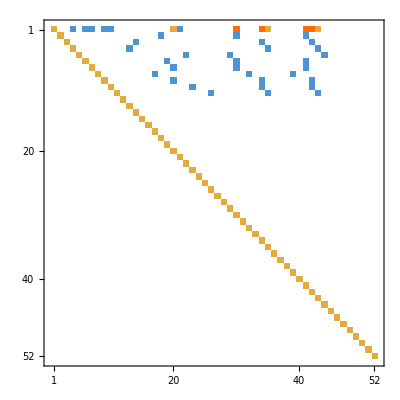

```mathematica
cyclemob=Map[
Table[Coefficient[#[[2]],t],{t,cycleSyms}]&,
cyclesols];MatrixPlot[cyclemob]
```

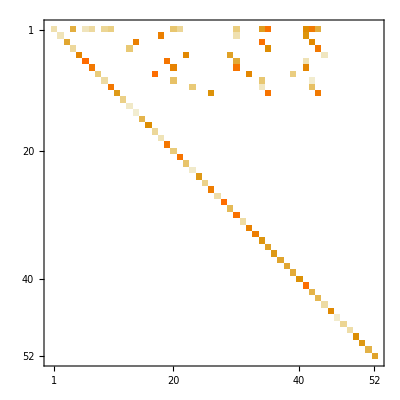

```mathematica
reoT=Map[Map[If[#==0,0,RandomInteger[{100,1000}]]&,#]&,cyclemob];MatrixPlot[reoT]
```

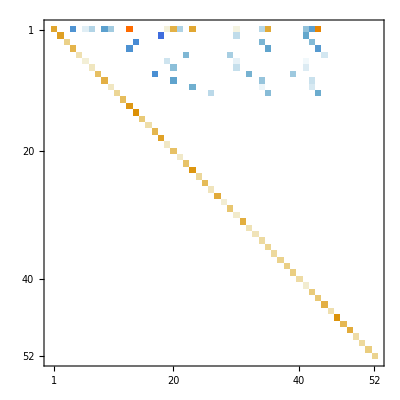

```mathematica
Inverse[reoT]//MatrixPlot
```

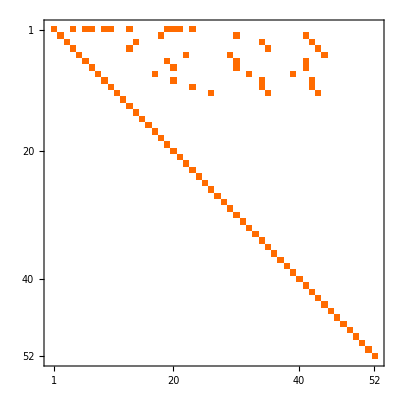

```mathematica
MatrixPlot[Inverse[cyclemob]]
```